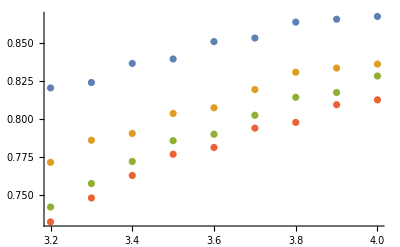

```mathematica
a={{3.2,84/(3.2×32)},{3.3,87/(3.3×32)},{3.4,91/(3.4×32)},{3.5,94/(3.5×32)}, {3.6,98/(3.6×32)},{3.7,101/(3.7×32)},{3.8,105/(3.8×32)}, {3.9,108/(3.9×32)},{4.0,111/(4×32)}};
a2={{3.2,79/(3.2×32)},{3.3,83/(3.3×32)},{3.4,86/(3.4×32)},{3.5,90/(3.5×32)}, {3.6,93/(3.6×32)},{3.7,97/(3.7×32)},{3.8,101/(3.8×32)}, {3.9,104/(3.9×32)},{4.0,107/(4×32)}};
a3={{3.2,76/(3.2×32)},{3.3,80/(3.3×32)},{3.4,84/(3.4×32)},{3.5,88/(3.5×32)}, {3.6,91/(3.6×32)},{3.7,95/(3.7×32)},{3.8,99/(3.8×32)}, {3.9,102/(3.9×32)},{4.0,106/(4×32)}};
a4={{3.2,75/(3.2×32)},{3.3,79/(3.3×32)},{3.4,83/(3.4×32)},{3.5,87/(3.5×32)}, {3.6,90/(3.6×32)},{3.7,94/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,101/(3.9×32)},{4.0,104/(4×32)}};
ListPlot[{a,a2,a3,a4}]
```

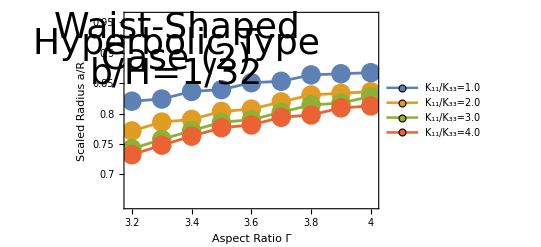

```mathematica
ListPlot[{a,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.70,0.75,0.80,0.85,0.9,0.95},None},{{3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.19,4.01},{0.65,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Right, Bottom}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{3.35,0.94}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.35,0.915}],Text[Style["Case (2)",Directive[Black,36]],{3.35,0.89}],Text[Style["b/H=1/32",Directive[Black,36]],{3.35,0.865}]}]
```